#### Get files

```mathematica
SetDirectory["C:\\Users\\mikol\\Dropbox\\UJ\\symulacje\\C60_Graph_hit_analysis\\data"]
```

C:\Users\mikol\Dropbox\UJ\symulacje\C60_Graph_hit_analysis\data

```mathematica
allfiles=Map[
<|"path"->#,"id"->StringSplit[FileBaseName[#],"_"]|>&
,FileNames["*.txt","",Infinity]];
```

```mathematica
Length[allfiles]
```

2710

```mathematica
%/5//N
```

542.

```mathematica
data=<||>;
Scan[
With[{key=#["id"]⟦1;;3⟧},
If[!KeyExistsQ[data,key],
data[key]=<|
"files"-><|"massspectrum"->{},"angledist"->{},"energies"->{},"masses"->{},"spotplot"->{}|>,
"results"-><||>
|>
];
AppendTo[data[key]["files"][#["id"]⟦-1⟧],#["path"]];
]&,
allfiles]
```

```mathematica
datakeys=Keys[data];
```

```mathematica
Table[{datakeys⟦i⟧,Length[data[datakeys⟦i⟧]["files"]["massspectrum"]]},{i,Length[datakeys]}]
```

{{{05keV,1L,00deg},12},{{05keV,2L,00deg},16},{{05keV,4L,00deg},17},{{05keV,6L,00deg},12},{{10keV,12L,00deg},7},{{10keV,1L,00deg},8},{{10keV,2L,00deg},52},{{10keV,4L,00deg},49},{{10keV,6L,00deg},12},{{10keV,8L,00deg},8},{{20keV,12L,00deg},7},{{20keV,16L,00deg},13},{{20keV,4L,00deg},16},{{20keV,6L,00deg},14},{{40keV,12L,00deg},7},{{40keV,16L,00deg},5},{{40keV,1L,00deg},7},{{40keV,4L,00deg},12},{{40keV,6L,00deg},7},{{10keV,2L,15deg},8},{{10keV,2L,30deg},8},{{10keV,1L,45deg},8},{{10keV,2L,45deg},7},{{10keV,4L,45deg},8},{{10keV,6L,45deg},8},{{10keV,2L,50deg},8},{{10keV,2L,55deg},7},{{10keV,2L,60deg},8},{{10keV,2L,65deg},8},{{10keV,2L,70deg},8},{{10keV,2L,75deg},8},{{10keV,2L,80deg},8},{{40keV,2L,00deg},8},{{40keV,8L,00deg},8},{{40keV,2L,15deg},7},{{40keV,8L,15deg},6},{{40keV,2L,30deg},7},{{40keV,8L,30deg},7},{{40keV,12L,45deg},8},{{40keV,16L,45deg},6},{{40keV,1L,45deg},7},{{40keV,2L,45deg},7},{{40keV,4L,45deg},7},{{40keV,8L,45deg},8},{{40keV,2L,55deg},8},{{40keV,16L,60deg},5},{{40keV,2L,60deg},8},{{40keV,8L,60deg},8},{{40keV,2L,65deg},8},{{40keV,2L,70deg},8},{{40keV,8L,70deg},6},{{40keV,2L,75deg},8},{{40keV,2L,77deg},6},{{40keV,2L,80deg},8}}

#### Get mass spectra from files

```mathematica
Scan[
Block[{massspectrum,import,topposition,bottomposition,topall,bottomall,top,bottom,toprelative,bottomrelative},
massspectrum=data[#]["files"]["massspectrum"];

import=Map[Import[#,"Table"]&,massspectrum];

topposition=Map[Flatten[Position[#,"Top"]]⟦1⟧&,import];
bottomposition=Map[Flatten[Position[#,"Bottom"]]⟦1⟧&,import];

topall=Table[import⟦i,topposition⟦i⟧+1;;bottomposition⟦i⟧-1,{1,2}⟧,{i,Length[import]}];
bottomall=Table[import⟦i,bottomposition⟦i⟧+1;;,{1,2}⟧,{i,Length[import]}];

top={};
Scan[
Scan[
With[{position=FirstPosition[top,#⟦1⟧]},
If[MissingQ[position],
AppendTo[top,#],
top⟦position⟦1⟧,2⟧+=#⟦2⟧
]
]&
,#]&
,topall];

bottom={};
Scan[
Scan[
With[{position=FirstPosition[bottom,#⟦1⟧]},
If[MissingQ[position],
AppendTo[bottom,#],
bottom⟦position⟦1⟧,2⟧+=#⟦2⟧
]
]&
,#]&
,bottomall];

toprelative=Transpose[{top⟦;;,1⟧,top⟦;;,2⟧/Max[top⟦;;,2⟧]}];
bottomrelative=Transpose[{bottom⟦;;,1⟧,bottom⟦;;,2⟧/Max[bottom⟦;;,2⟧]}];

data[#]["results"]["massspectrum"]=<|
"top"->top,
"bottom"->bottom,
"toprelative"->toprelative,
"bottomrelative"->bottomrelative
|>
]&
,datakeys]
```

#### Get yields

```mathematica
Scan[
Block[{masses, import,topposition,bottomposition,topall,bottomall,topC60,bottomC60,topGraph,bottomGraph,topC60MassYield,bottomC60MassYield,topC60NumberYield,bottomC60NumberYield,topGraphMassYield,bottomGraphMassYield,topGraphNumberYield,bottomGraphNumberYield},
masses=data[#]["files"]["masses"];

import=Map[Import[#,"Table"]&,masses];

topposition=Map[Flatten[Position[#,"Top"]]⟦1⟧&,import];
bottomposition=Map[Flatten[Position[#,"Bottom"]]⟦1⟧&,import];

topall=Table[import⟦i,topposition⟦i⟧+1;;bottomposition⟦i⟧-1,{3}⟧,{i,Length[import]}];
bottomall=Table[import⟦i,bottomposition⟦i⟧+1;;,{3}⟧,{i,Length[import]}];

topC60=Flatten[topall⟦;;,2⟧];
topGraph=Flatten[topall⟦;;,3⟧];
bottomC60=Flatten[bottomall⟦;;,2⟧];
bottomGraph=Flatten[bottomall⟦;;,3⟧];

topC60MassYield={Mean[topC60],If[Length[topC60]≥2,StandardDeviation[topC60],0]/Sqrt[Length[topC60]]};
topGraphMassYield={Mean[topGraph],If[Length[topC60]≥2,StandardDeviation[topGraph],0]/Sqrt[Length[topGraph]]};
bottomC60MassYield={Mean[bottomC60],If[Length[topC60]≥2,StandardDeviation[bottomC60],0]/Sqrt[Length[bottomC60]]};
bottomGraphMassYield={Mean[bottomGraph],If[Length[topC60]≥2,StandardDeviation[bottomGraph],0]/Sqrt[Length[bottomGraph]]};

topC60NumberYield=topC60MassYield/12.011;
topGraphNumberYield=topGraphMassYield/12.011;
bottomC60NumberYield=bottomC60MassYield/12.011;
bottomGraphNumberYield=bottomGraphMassYield/12.011;

data[#]["results"]["yield"]=<|
"topmass"-><|"C60"->topC60MassYield,"Graph"->topGraphMassYield|>,
"bottommass"-><|"C60"->bottomC60MassYield,"Graph"->bottomGraphMassYield|>,
"topnumber"-><|"C60"->topC60NumberYield,"Graph"->topGraphNumberYield|>,
"bottomnumber"-><|"C60"->bottomC60NumberYield,"Graph"->bottomGraphNumberYield|>
|>
]&
,datakeys]
```

#### Get angle distributions

```mathematica
Scan[
Block[{angledist,import,topposition,bottomposition,topall,bottomall,dphi,top,bottom,topkeys,bottomkeys,toprelative,bottomrelative,max},
angledist=data[#]["files"]["angledist"];

import=Map[Import[#,"Table"]&,angledist];

topposition=Map[Flatten[Position[#,"Top"]]⟦1⟧&,import];
bottomposition=Map[Flatten[Position[#,"Bottom"]]⟦1⟧&,import];

topall=Table[import⟦i,topposition⟦i⟧+1;;bottomposition⟦i⟧-1⟧,{i,Length[import]}];
bottomall=Table[import⟦i,bottomposition⟦i⟧+1;;⟧,{i,Length[import]}];

dphi=Map[#⟦1,3⟧&,import];

top=<||>;
Scan[
Scan[
If[KeyExistsQ[top,#⟦1⟧],
top[#⟦1⟧]=top[#⟦1⟧]+PadRight[#⟦2;;⟧,30];,
top[#⟦1⟧]=PadRight[#⟦2;;⟧,30];
]&
,#]&
,topall];
topkeys=Keys[top];
top["all"]=ConstantArray[0,30];
Scan[
top["all"]=top["all"]+top[#];&
,topkeys];

topkeys=Keys[top];
Scan[
top[#]=Transpose[{Range[0,Length[top[#]]-1,1]*dphi⟦1⟧*180/π,top[#]}];&
,topkeys];

topkeys=Keys[top];
toprelative=<||>;
Scan[
If[Max[top[#]⟦;;,2⟧]==0,
max=1,
max=Max[top[#]⟦;;,2⟧]
];
toprelative[#]=Transpose[{top[#]⟦;;,1⟧,top[#]⟦;;,2⟧/max}];&
,topkeys];

bottom=<||>;
Scan[
Scan[
If[KeyExistsQ[bottom,#⟦1⟧],
bottom[#⟦1⟧]=bottom[#⟦1⟧]+PadRight[#⟦2;;⟧,30];,
bottom[#⟦1⟧]=PadRight[#⟦2;;⟧,30];
]&
,#]&
,bottomall];
bottomkeys=Keys[bottom];
bottom["all"]=ConstantArray[0,30];
Scan[
bottom["all"]=bottom["all"]+bottom[#];&
,bottomkeys];

bottomkeys=Keys[bottom];
Scan[
bottom[#]=Transpose[{Range[0,Length[bottom[#]]-1,1]*dphi⟦1⟧*180/π,bottom[#]}];&
,bottomkeys];

bottomkeys=Keys[bottom];
bottomrelative=<||>;
Scan[
If[Max[bottom[#]⟦;;,2⟧]==0,
max=1,
max=Max[bottom[#]⟦;;,2⟧]
];
bottomrelative[#]=Transpose[{bottom[#]⟦;;,1⟧,bottom[#]⟦;;,2⟧/max}];&
,bottomkeys];

data[#]["results"]["angledist"]=<|
"top"->top,
"toprelative"->toprelative,
"bottom"->bottom,
"bottomrelative"->bottomrelative
|>
]&
,datakeys]
```

#### Get energy distributions

```mathematica
Scan[
Block[{energies,import,topposition,bottomposition,topall,bottomall,toptotal,topinternal,toptranslational,bottomtotal,bottominternal,bottomtranslational},
energies=data[#]["files"]["energies"];

import=Map[Import[#,"Table"]&,energies];

topposition=Map[Flatten[Position[#,"Top"]]⟦1⟧&,import];
bottomposition=Map[Flatten[Position[#,"Bottom"]]⟦1⟧&,import];

topall=Table[import⟦i,topposition⟦i⟧+1;;bottomposition⟦i⟧-1⟧,{i,Length[import]}];
bottomall=Table[import⟦i,bottomposition⟦i⟧+1;;⟧,{i,Length[import]}];

toptotal=Flatten[topall⟦;;,;;,1⟧];
topinternal=Flatten[topall⟦;;,;;,2⟧];
toptranslational=Flatten[topall⟦;;,;;,3⟧];
bottomtotal=Flatten[bottomall⟦;;,;;,1⟧];
bottominternal=Flatten[bottomall⟦;;,;;,2⟧];
bottomtranslational=Flatten[bottomall⟦;;,;;,3⟧];

data[#]["results"]["energies"]=<|
"top"-><|"total"->toptotal,"internal"->topinternal,"translational"->toptranslational|>,
"bottom"-><|"total"->bottomtotal,"internal"->bottominternal,"translational"->bottomtranslational|>
|>
]&
,datakeys]
```

#### Get interesting datakeys

```mathematica
Union[datakeys⟦;;,1⟧]
```

{05keV,10keV,20keV,40keV}

```mathematica
layers={"1L","2L","4L","6L","8L","12L","16L"};
energies={"05keV","10keV","20keV","40keV"};
angles={"00deg","15deg","30deg","45deg","50deg","55deg","60deg","65deg","70deg","75deg","77deg","80deg"};
```

```mathematica
energiessweep=Table[Select[datakeys,#⟦2⟧==layers⟦i⟧&&#⟦3⟧=="00deg"&],{i,Length[layers]}];
```

```mathematica
layerssweep=Table[SortBy[Select[datakeys,#⟦1⟧==energies⟦i⟧&&#⟦3⟧=="00deg"&],Position[layers,#⟦2⟧]&],{i,Length[energies]}];
```

```mathematica
layerssweep45=Table[SortBy[Select[datakeys,#⟦1⟧==energies⟦i⟧&&#⟦3⟧=="45deg"&],Position[layers,#⟦2⟧]&],{i,Length[energies]}]//.{}->Sequence[];
```

```mathematica
anglessweep={Select[datakeys,#⟦1⟧=="10keV"&&#⟦2⟧=="2L"&],Select[datakeys,#⟦1⟧=="40keV"&&#⟦2⟧=="2L"&]};
```

#### Show yields

```mathematica
ejection=Column[
{
"Ejection - number of C atoms",
Grid[
Join[
{Join[{""},energies]},
Table[
Prepend[
Table[
Grid[
{
{
"C60:",
If[MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
"---",
ToString[NumberForm[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["C60"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["C60"]⟦2⟧,{Infinity,2}]]
]
},
{
"Graph:",
If[MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
"---",
ToString[NumberForm[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦2⟧,{Infinity,2}]]
]
}
},
Alignment->{{Right,"±"}}
],
{i,Length[energies]}
],
layers⟦j⟧
],
{j,Length[layers]}
]
],
Alignment->Left,
Spacings->{2, 1},
Dividers->{2->True,2->True}
]
},
Alignment->Center
]
```

Ejection - number of C atoms
 | 05keV | 10keV | 20keV | 40keV
1L | C60: | 60.00±0.00
Graph: | 21.50±0.61 | C60: | 60.00±0.00
Graph: | 19.75±0.77 | C60: | ---
Graph: | --- | C60: | 59.86±0.14
Graph: | 15.43±0.92
2L | C60: | 57.00±0.32
Graph: | 55.50±1.12 | C60: | 56.67±1.13
Graph: | 48.17±1.22 | C60: | ---
Graph: | --- | C60: | 58.75±0.37
Graph: | 41.50±2.15
4L | C60: | 39.24±0.78
Graph: | 132.18±2.67 | C60: | 45.37±1.41
Graph: | 151.06±4.92 | C60: | 52.25±0.74
Graph: | 166.31±4.32 | C60: | 53.67±0.68
Graph: | 149.92±8.39
6L | C60: | 13.42±1.11
Graph: | 82.67±3.75 | C60: | 30.08±1.21
Graph: | 255.42±7.97 | C60: | 40.43±1.19
Graph: | 322.00±10.86 | C60: | 49.29±0.99
Graph: | 339.71±21.11
8L | C60: | ---
Graph: | --- | C60: | 13.00±1.16
Graph: | 167.25±6.68 | C60: | ---
Graph: | --- | C60: | 40.75±0.82
Graph: | 612.13±21.38
12L | C60: | ---
Graph: | --- | C60: | 0.00±0.00
Graph: | 0.29±0.18 | C60: | 2.86±0.63
Graph: | 42.14±17.28 | C60: | 22.86±0.96
Graph: | 761.43±22.28
16L | C60: | ---
Graph: | --- | C60: | ---
Graph: | --- | C60: | 0.69±0.21
Graph: | 0.62±0.27 | C60: | 4.20±1.20
Graph: | 52.40±33.94

```mathematica
Rasterize[ejection]
```

-Graphics-

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
energiesplot={0.5,10,20,40};
layersplot={1,2,4,6,8,12,16};
```

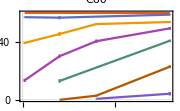

```mathematica
inset=ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
{{energiesplot⟦i⟧,data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["C60"]⟦1⟧},ErrorBar[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["C60"]⟦2⟧]},{}],
{i,Length[energies]}
],
{j,Length[layers]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
ImageSize->Small,
PlotLabel->"C60"
]
```

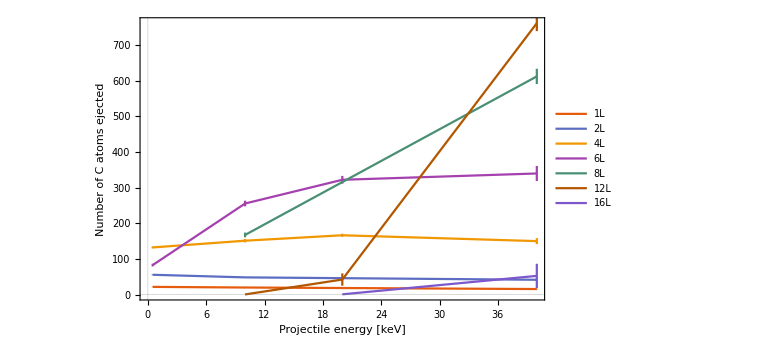

```mathematica
ejectionplot=Show[
ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
{{energiesplot⟦i⟧,data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦1⟧},ErrorBar[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦2⟧]},{}],
{i,Length[energies]}
],
{j,Length[layers]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
FrameLabel->{"Projectile energy [keV]","Number of C atoms ejected"},
PlotLegends->Placed[layers,Top],
ImageSize->Large
],
Epilog->Inset[inset,Scaled[{0.2,0.75}]]
]
```

```mathematica
Rasterize[ejectionplot]
```

-Graphics-

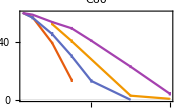

```mathematica
inset=ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
{{layersplot⟦j⟧,data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["C60"]⟦1⟧},ErrorBar[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["C60"]⟦2⟧]},{}],
{j,Length[layers]}
],
{i,Length[energies]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
ImageSize->Small,
PlotLabel->"C60"
]
```

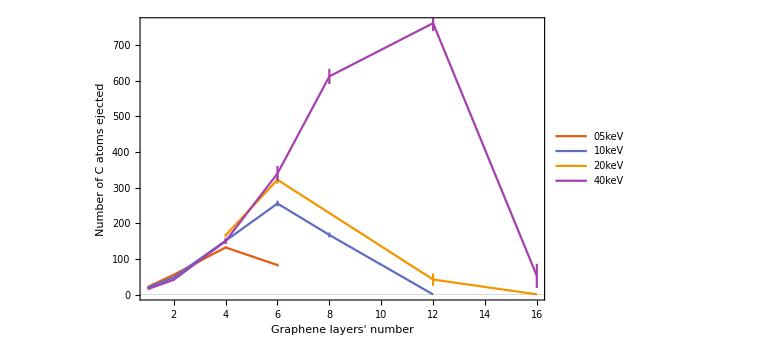

```mathematica
ejectionplot=Show[
ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
{{layersplot⟦j⟧,data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦1⟧},ErrorBar[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦2⟧]},{}],
{j,Length[layers]}
],
{i,Length[energies]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
FrameLabel->{"Graphene layers' number","Number of C atoms ejected"},
PlotLegends->Placed[energies,Top],
ImageSize->Large
],
Epilog->Inset[inset,Scaled[{0.2,0.75}]]
]
```

```mathematica
Rasterize[ejectionplot]
```

-Graphics-

```mathematica
reflection=Column[
{
"Reflection - number of C atoms",
Grid[
Join[
{Join[{""},energies]},
Table[
Prepend[
Table[
Grid[
{
{
"C60:",
If[MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
"---",
ToString[NumberForm[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦2⟧,{Infinity,2}]]
]
},
{
"Graph:",
If[MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
"---",
ToString[NumberForm[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦2⟧,{Infinity,2}]]
]
}
},
Alignment->{{Right,"±"}}
],
{i,Length[energies]}
],
layers⟦j⟧
],
{j,Length[layers]}
]
],
Alignment->Left,
Spacings->{2, 1},
Dividers->{2->True,2->True}
]
},
Alignment->Center
]
```

Reflection - number of C atoms
 | 05keV | 10keV | 20keV | 40keV
1L | C60: | 0.00±0.00
Graph: | 0.00±0.00 | C60: | 0.00±0.00
Graph: | 0.13±0.13 | C60: | ---
Graph: | --- | C60: | 0.14±0.14
Graph: | 1.86±0.86
2L | C60: | 0.00±0.00
Graph: | 0.00±0.00 | C60: | 0.10±0.04
Graph: | 0.40±0.12 | C60: | ---
Graph: | --- | C60: | 0.00±0.00
Graph: | 3.75±0.59
4L | C60: | 0.00±0.00
Graph: | 0.12±0.12 | C60: | 0.10±0.04
Graph: | 0.61±0.17 | C60: | 0.31±0.15
Graph: | 2.06±0.38 | C60: | 0.00±0.00
Graph: | 7.75±0.77
6L | C60: | 0.58±0.29
Graph: | 0.42±0.19 | C60: | 0.17±0.11
Graph: | 1.25±0.45 | C60: | 0.07±0.07
Graph: | 4.21±0.74 | C60: | 0.29±0.18
Graph: | 8.14±2.10
8L | C60: | ---
Graph: | --- | C60: | 0.50±0.27
Graph: | 0.75±0.41 | C60: | ---
Graph: | --- | C60: | 0.13±0.13
Graph: | 13.50±2.85
12L | C60: | ---
Graph: | --- | C60: | 0.14±0.14
Graph: | 0.57±0.37 | C60: | 0.00±0.00
Graph: | 6.29±1.58 | C60: | 0.14±0.14
Graph: | 18.71±3.23
16L | C60: | ---
Graph: | --- | C60: | ---
Graph: | --- | C60: | 0.31±0.13
Graph: | 4.54±1.01 | C60: | 0.40±0.24
Graph: | 13.00±4.36

```mathematica
Rasterize[reflection]
```

-Graphics-

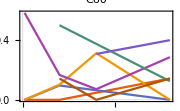

```mathematica
inset=ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
{{energiesplot⟦i⟧,data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦1⟧},ErrorBar[0.0(*data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦2⟧*)]},{}],
{i,Length[energies]}
],
{j,Length[layers]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
ImageSize->Small,
PlotLabel->"C60"
]
```

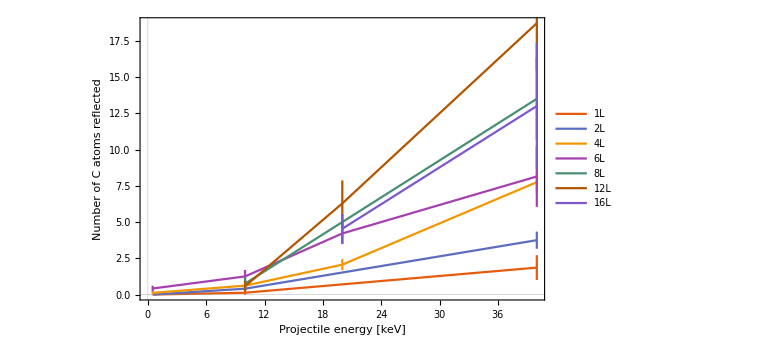

```mathematica
reflectionplot=Show[
ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
{{energiesplot⟦i⟧,data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦1⟧},ErrorBar[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦2⟧]},{}],
{i,Length[energies]}
],
{j,Length[layers]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
FrameLabel->{"Projectile energy [keV]","Number of C atoms reflected"},
PlotLegends->Placed[layers,Top],
ImageSize->Large
],
Epilog->Inset[inset,Scaled[{0.2,0.75}]]
]
```

```mathematica
Rasterize[reflectionplot]
```

-Graphics-

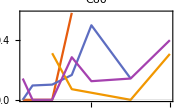

```mathematica
inset=ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
{{layersplot⟦j⟧,data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦1⟧},ErrorBar[0.0(*data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦2⟧*)]},{}],
{j,Length[layers]}
],
{i,Length[energies]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
ImageSize->Small,
PlotLabel->"C60"
]
```

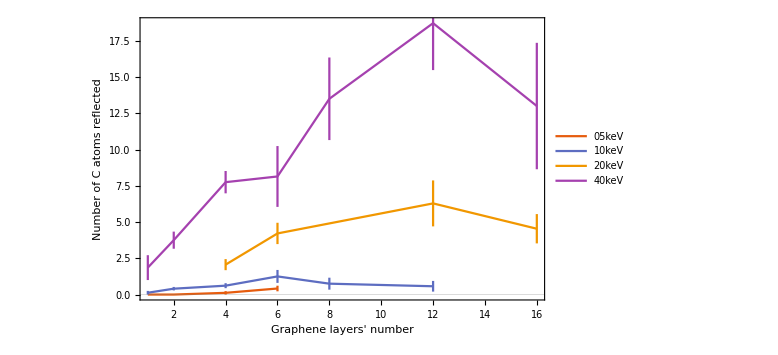

```mathematica
reflectionplot=Show[
ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
{{layersplot⟦j⟧,data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦1⟧},ErrorBar[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦2⟧]},{}],
{j,Length[layers]}
],
{i,Length[energies]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
FrameLabel->{"Graphene layers' number","Number of C atoms reflected"},
PlotLegends->Placed[energies,Top],
ImageSize->Large
],
Epilog->Inset[inset,Scaled[{0.2,0.75}]]
]
```

```mathematica
Rasterize[reflectionplot]
```

-Graphics-

```mathematica
energiesangleplot={10,40};
layersplot={1,2,4,6,8,12,16};
```

```mathematica
energiesangle={"10keV","40keV"};
```

```mathematica
anglesplot={0,15,30,45,50,55,60,65,70,75,77,80};
```

```mathematica
ejection=Column[
{
"Ejection - number of C atoms",
Grid[
Join[
{Join[{""},energiesangle]},
Table[
Prepend[
Table[
Grid[
{
{
"C60:",
If[MissingQ[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["topnumber"]["C60"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["topnumber"]["C60"]⟦2⟧,{Infinity,2}]]
]
},
{
"Graph:",
If[MissingQ[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦2⟧,{Infinity,2}]]
]
}
},
Alignment->{{Right,"±"}}
],
{i,Length[energiesangle]}
],
layers⟦j⟧
],
{j,Length[layers]}
]
],
Alignment->Left,
Spacings->{2, 1},
Dividers->{2->True,2->True}
]
},
Alignment->Center
]
```

Ejection - number of C atoms
 | 10keV | 40keV
1L | C60: | 53.50±0.76
Graph: | 31.13±1.11 | C60: | 57.71±0.36
Graph: | 23.86±1.45
2L | C60: | 46.43±1.25
Graph: | 83.43±1.43 | C60: | 54.43±1.17
Graph: | 68.71±4.94
4L | C60: | 25.25±0.88
Graph: | 210.37±4.86 | C60: | 43.71±1.08
Graph: | 263.29±10.94
6L | C60: | 11.88±1.49
Graph: | 173.62±9.62 | C60: | ---
Graph: | ---
8L | C60: | ---
Graph: | --- | C60: | 27.25±1.19
Graph: | 744.25±15.08
12L | C60: | ---
Graph: | --- | C60: | 7.50±1.48
Graph: | 280.87±16.86
16L | C60: | ---
Graph: | --- | C60: | 1.17±0.31
Graph: | 5.83±0.95

```mathematica
Rasterize[ejection]
```

-Graphics-

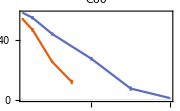

```mathematica
inset=ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]],
{{layersplot⟦j⟧,data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["topnumber"]["C60"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["topnumber"]["C60"]⟦2⟧]},{}],
{j,Length[layers]}
],
{i,Length[energiesangle]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
ImageSize->Small,
PlotLabel->"C60"
]
```

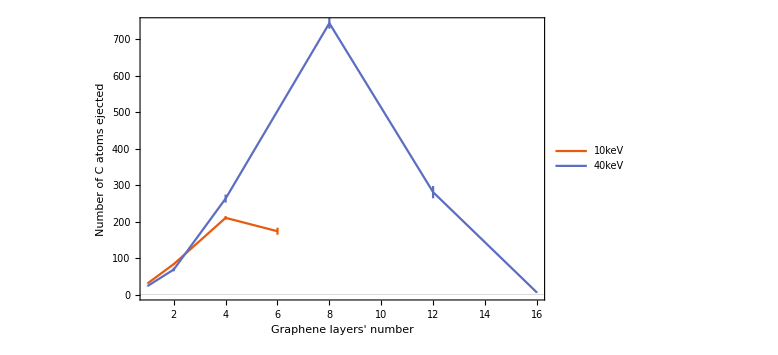

```mathematica
ejectionplot=Show[
ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]],
{{layersplot⟦j⟧,data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦2⟧]},{}],
{j,Length[layers]}
],
{i,Length[energiesangle]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
FrameLabel->{"Graphene layers' number","Number of C atoms ejected"},
PlotLegends->Placed[energiesangle,Top],
ImageSize->Large
],
Epilog->Inset[inset,Scaled[{0.2,0.75}]]
]
```

```mathematica
Rasterize[ejectionplot]
```

-Graphics-

```mathematica
reflection=Column[
{
"Reflection - number of C atoms",
Grid[
Join[
{Join[{""},energiesangle]},
Table[
Prepend[
Table[
Grid[
{
{
"C60:",
If[MissingQ[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦2⟧,{Infinity,2}]]
]
},
{
"Graph:",
If[MissingQ[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦2⟧,{Infinity,2}]]
]
}
},
Alignment->{{Right,"±"}}
],
{i,Length[energiesangle]}
],
layers⟦j⟧
],
{j,Length[layers]}
]
],
Alignment->Left,
Spacings->{2, 1},
Dividers->{2->True,2->True}
]
},
Alignment->Center
]
```

Reflection - number of C atoms
 | 10keV | 40keV
1L | C60: | 5.13±0.79
Graph: | 11.00±1.07 | C60: | 2.14±0.34
Graph: | 13.00±1.05
2L | C60: | 5.71±0.84
Graph: | 30.86±3.61 | C60: | 3.43±0.65
Graph: | 36.71±6.73
4L | C60: | 8.25±1.08
Graph: | 53.25±6.30 | C60: | 5.00±0.76
Graph: | 116.57±11.19
6L | C60: | 9.25±0.96
Graph: | 63.25±4.26 | C60: | ---
Graph: | ---
8L | C60: | ---
Graph: | --- | C60: | 5.75±0.84
Graph: | 240.75±16.27
12L | C60: | ---
Graph: | --- | C60: | 7.00±0.76
Graph: | 286.25±33.69
16L | C60: | ---
Graph: | --- | C60: | 7.00±0.73
Graph: | 292.17±18.41

```mathematica
Rasterize[reflection]
```

-Graphics-

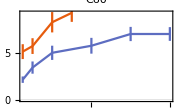

```mathematica
inset=ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]],
{{layersplot⟦j⟧,data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦2⟧]},{}],
{j,Length[layers]}
],
{i,Length[energiesangle]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
ImageSize->Small,
PlotLabel->"C60"
]
```

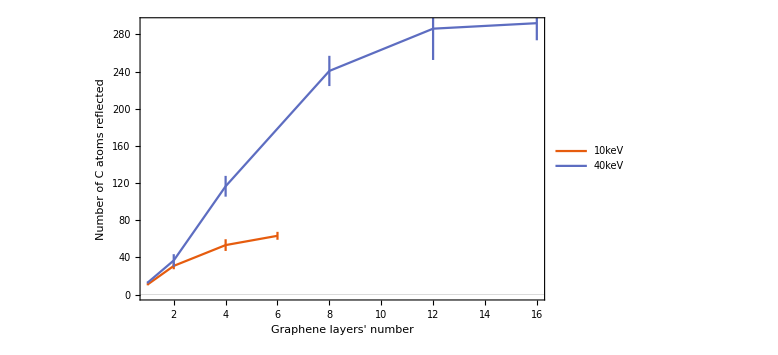

```mathematica
reflectionplot=Show[
ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]],
{{layersplot⟦j⟧,data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦2⟧]},{}],
{j,Length[layers]}
],
{i,Length[energiesangle]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
FrameLabel->{"Graphene layers' number","Number of C atoms reflected"},
PlotLegends->Placed[energiesangle,Top],
ImageSize->Large
],
Epilog->Inset[inset,Scaled[{0.2,0.75}]]
]
```

```mathematica
Rasterize[reflectionplot]
```

-Graphics-

```mathematica
ejection=Column[
{
"Ejection - number of C atoms",
Grid[
Join[
{Join[{""},energiesangle]},
Table[
Prepend[
Table[
Grid[
{
{
"C60:",
If[MissingQ[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["C60"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["C60"]⟦2⟧,{Infinity,2}]]
]
},
{
"Graph:",
If[MissingQ[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["Graph"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["Graph"]⟦2⟧,{Infinity,2}]]
]
}
},
Alignment->{{Right,"±"}}
],
{i,Length[energiesangle]}
],
angles⟦j⟧
],
{j,Length[angles]}
]
],
Alignment->Left,
Spacings->{1, 1},
Dividers->{2->True,2->True}
]
},
Alignment->Center
]
```

Ejection - number of C atoms
 | 10keV | 40keV
00deg | C60: | 56.67±1.13
Graph: | 48.17±1.22 | C60: | 58.75±0.37
Graph: | 41.50±2.15
15deg | C60: | 57.13±0.83
Graph: | 50.50±1.56 | C60: | 58.29±0.57
Graph: | 42.43±1.91
30deg | C60: | 53.63±0.65
Graph: | 65.62±2.31 | C60: | 58.00±0.58
Graph: | 58.71±4.44
45deg | C60: | 46.43±1.25
Graph: | 83.43±1.43 | C60: | 54.43±1.17
Graph: | 68.71±4.94
50deg | C60: | 37.63±1.00
Graph: | 97.62±3.84 | C60: | ---
Graph: | ---
55deg | C60: | 30.43±1.13
Graph: | 115.14±3.10 | C60: | 46.63±1.00
Graph: | 98.75±4.04
60deg | C60: | 19.00±1.00
Graph: | 124.12±3.81 | C60: | 39.13±1.79
Graph: | 122.37±5.93
65deg | C60: | 8.62±0.71
Graph: | 121.87±2.07 | C60: | 30.88±1.04
Graph: | 137.37±4.96
70deg | C60: | 3.13±0.44
Graph: | 80.87±4.51 | C60: | 17.63±0.75
Graph: | 165.50±4.26
75deg | C60: | 0.50±0.19
Graph: | 20.88±1.60 | C60: | 7.88±1.46
Graph: | 187.00±7.06
77deg | C60: | ---
Graph: | --- | C60: | 2.50±0.62
Graph: | 150.67±10.71
80deg | C60: | 1.63±0.53
Graph: | 0.00±0.00 | C60: | 0.25±0.16
Graph: | 28.63±5.53

```mathematica
Rasterize[ejection]
```

-Graphics-

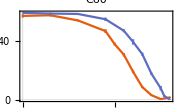

```mathematica
inset=ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]],
{{anglesplot⟦j⟧,data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["C60"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["C60"]⟦2⟧]},{}],
{j,Length[angles]}
],
{i,Length[energiesangle]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
ImageSize->Small,
PlotLabel->"C60"
]
```

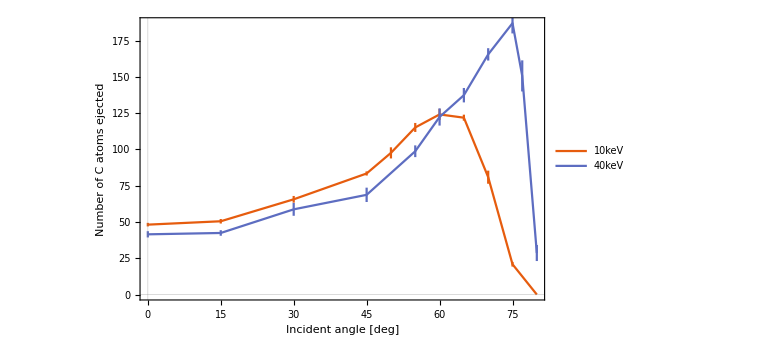

```mathematica
ejectionplot=Show[
ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]],
{{anglesplot⟦j⟧,data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["Graph"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["Graph"]⟦2⟧]},{}],
{j,Length[angles]}
],
{i,Length[energiesangle]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
FrameLabel->{"Incident angle [deg]","Number of C atoms ejected"},
PlotLegends->Placed[energiesangle,Top],
ImageSize->Large
],
Epilog->Inset[inset,Scaled[{0.2,0.75}]]
]
```

```mathematica
Rasterize[ejectionplot]
```

-Graphics-

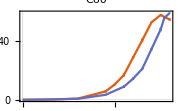

```mathematica
inset=ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]],
{{anglesplot⟦j⟧,data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["C60"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["C60"]⟦2⟧]},{}],
{j,Length[angles]}
],
{i,Length[energiesangle]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
ImageSize->Small,
PlotLabel->"C60"
]
```

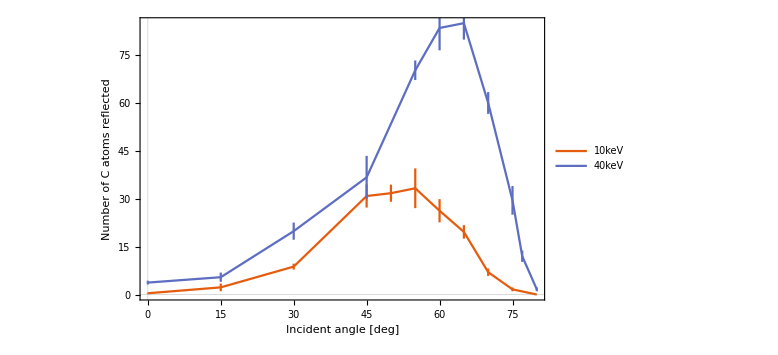

```mathematica
reflectionplot=Show[
ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]],
{{anglesplot⟦j⟧,data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["Graph"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["Graph"]⟦2⟧]},{}],
{j,Length[angles]}
],
{i,Length[energiesangle]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
FrameLabel->{"Incident angle [deg]","Number of C atoms reflected"},
PlotLegends->Placed[energiesangle,Top],
ImageSize->Large
],
Epilog->Inset[inset,Scaled[{0.2,0.75}]]
]
```

```mathematica
Rasterize[reflectionplot]
```

-Graphics-

```mathematica
reflection=Column[
{
"Reflection - number of C atoms",
Grid[
Join[
{Join[{""},energiesangle]},
Table[
Prepend[
Table[
Grid[
{
{
"C60:",
If[MissingQ[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["C60"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["C60"]⟦2⟧,{Infinity,2}]]
]
},
{
"Graph:",
If[MissingQ[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["Graph"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["Graph"]⟦2⟧,{Infinity,2}]]
]
}
},
Alignment->{{Right,"±"}}
],
{i,Length[energiesangle]}
],
angles⟦j⟧
],
{j,Length[angles]}
]
],
Alignment->Left,
Spacings->{1, 1},
Dividers->{2->True,2->True}
]
},
Alignment->Center
]
```

Reflection - number of C atoms
 | 10keV | 40keV
00deg | C60: | 0.10±0.04
Graph: | 0.40±0.12 | C60: | 0.00±0.00
Graph: | 3.75±0.59
15deg | C60: | 0.13±0.13
Graph: | 2.25±1.21 | C60: | 0.29±0.18
Graph: | 5.43±1.45
30deg | C60: | 0.88±0.40
Graph: | 8.75±0.92 | C60: | 0.71±0.47
Graph: | 19.86±2.69
45deg | C60: | 5.71±0.84
Graph: | 30.86±3.61 | C60: | 3.43±0.65
Graph: | 36.71±6.73
50deg | C60: | 10.50±0.60
Graph: | 31.75±2.68 | C60: | ---
Graph: | ---
55deg | C60: | 17.00±1.07
Graph: | 33.29±6.22 | C60: | 9.00±0.91
Graph: | 70.25±3.06
60deg | C60: | 29.00±0.98
Graph: | 26.25±3.63 | C60: | 14.50±0.98
Graph: | 83.50±7.00
65deg | C60: | 40.88±1.17
Graph: | 19.63±2.10 | C60: | 21.25±0.88
Graph: | 85.00±5.15
70deg | C60: | 53.13±0.52
Graph: | 7.00±1.16 | C60: | 34.75±0.90
Graph: | 60.00±3.41
75deg | C60: | 58.13±0.64
Graph: | 1.63±0.60 | C60: | 48.25±1.24
Graph: | 29.50±4.49
77deg | C60: | ---
Graph: | --- | C60: | 56.17±0.91
Graph: | 12.00±1.77
80deg | C60: | 55.00±0.78
Graph: | 0.00±0.00 | C60: | 59.62±0.18
Graph: | 1.63±0.60

```mathematica
Rasterize[reflection]
```

-Graphics-

#### Plot mass spectra

```mathematica
massspectrumPlotTheme={
PlotTheme->"Scientific",
(*PlotRange->All,*)
(*Filling->Bottom,*)
FillingStyle->Opacity[1],
PlotStyle->PointSize[Tiny],
FrameLabel->{"Mass",(*"Relative abundace [a.u.]"*)None}
};
```

```mathematica
move[i_]:=(i-1)*1.2;
```

```mathematica
energiessweep
```

{{{05keV,1L,00deg},{10keV,1L,00deg},{40keV,1L,00deg}},{{05keV,2L,00deg},{10keV,2L,00deg},{40keV,2L,00deg}},{{05keV,4L,00deg},{10keV,4L,00deg},{20keV,4L,00deg},{40keV,4L,00deg}},{{05keV,6L,00deg},{10keV,6L,00deg},{20keV,6L,00deg},{40keV,6L,00deg}},{{10keV,8L,00deg},{40keV,8L,00deg}},{{10keV,12L,00deg},{20keV,12L,00deg},{40keV,12L,00deg}},{{20keV,16L,00deg},{40keV,16L,00deg}}}

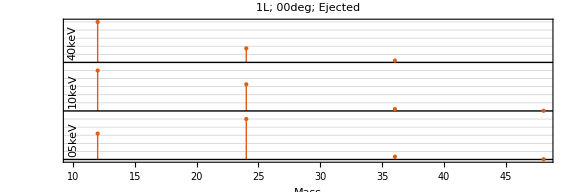
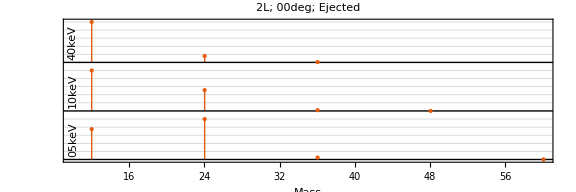
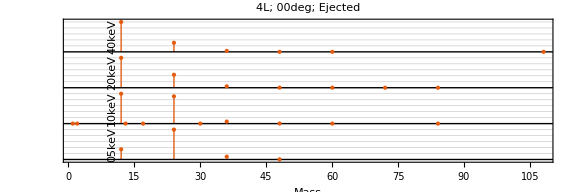
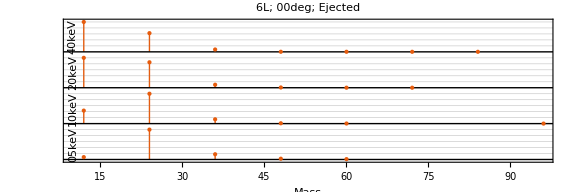
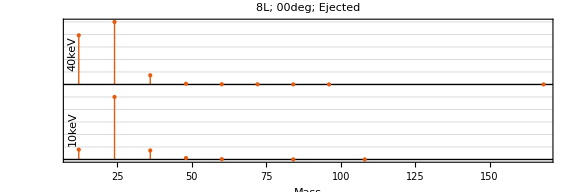
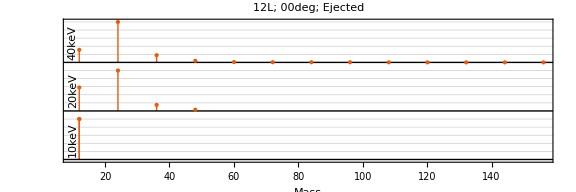
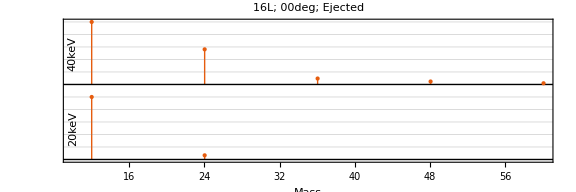

```mathematica
Table[
aaa=Table[
Show[
{
ListPlot[
Transpose[{data[energiessweep⟦j,i⟧]["results"]["massspectrum"]["toprelative"]⟦;;,1⟧,data[energiessweep⟦j,i⟧]["results"]["massspectrum"]["toprelative"]⟦;;,2⟧+move[i]}],
massspectrumPlotTheme,
Filling->move[i],
PlotRange->{All,{move[i],All}}
],
Graphics[{Thin,InfiniteLine[{{0,move[i]},{50,move[i]}}]}],
Graphics[Text[energiessweep⟦j,i,1⟧,{10,move[i]+0.5},{0,0},{0,1},Background->White]]
}
],
{i,Length[energiessweep⟦j⟧]}
];

Show[
aaa,
PlotRange->All,
GridLines->{None,Flatten[Table[Range[move[i]+0.2,move[i]+1,0.2],{i,1,Length[aaa],1}]]},
FrameTicks->{Automatic,None},
AspectRatio->1/3,
PlotLabel->StringJoin[Riffle[Flatten[{energiessweep⟦j,1,2;;3⟧,{"Ejected"}}],"; "]],
ImageSize->Large
],
{j,Length[energiessweep]}]
```

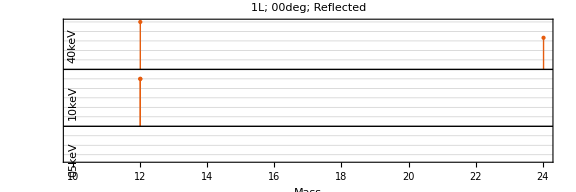
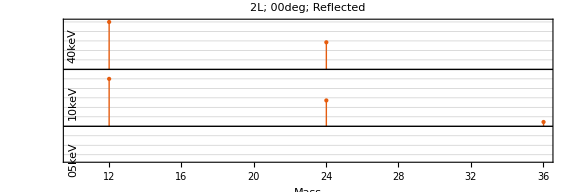
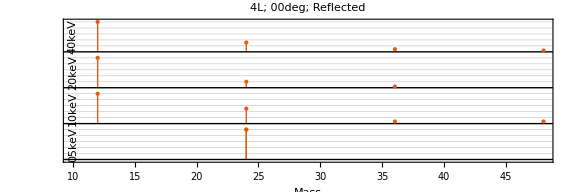
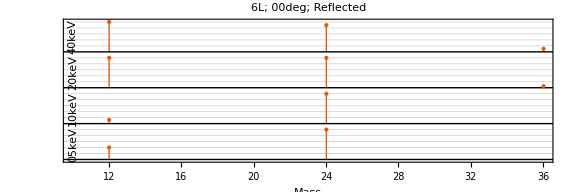
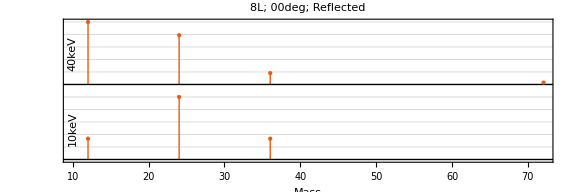
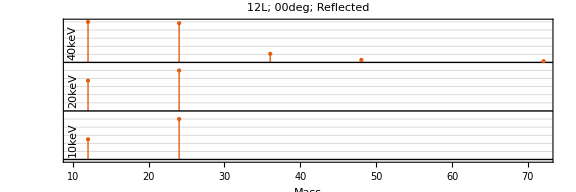
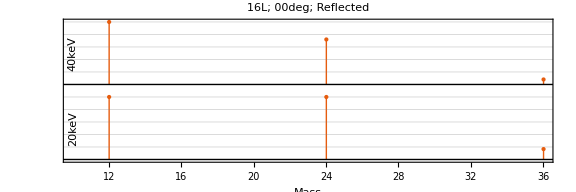

```mathematica
Table[
aaa=Table[
Show[
{
ListPlot[
Transpose[{data[energiessweep⟦j,i⟧]["results"]["massspectrum"]["bottomrelative"]⟦;;,1⟧,data[energiessweep⟦j,i⟧]["results"]["massspectrum"]["bottomrelative"]⟦;;,2⟧+move[i]}],
massspectrumPlotTheme,
Filling->move[i],
PlotRange->{All,{move[i],All}}
],
Graphics[{Thin,InfiniteLine[{{0,move[i]},{50,move[i]}}]}],
Graphics[Text[energiessweep⟦j,i,1⟧,{10,move[i]+0.5},{0,0},{0,1},Background->White]]
}
],
{i,Length[energiessweep⟦j⟧]}
];

Show[
aaa,
PlotRange->All,
GridLines->{None,Flatten[Table[Range[move[i]+0.2,move[i]+1,0.2],{i,1,Length[aaa],1}]]},
FrameTicks->{Automatic,None},
AspectRatio->1/3,
PlotLabel->StringJoin[Riffle[Flatten[{energiessweep⟦j,1,2;;3⟧,{"Reflected"}}],"; "]],
ImageSize->Large
],
{j,Length[energiessweep]}]
```

```mathematica
layerssweep
```

{{{05keV,1L,00deg},{05keV,2L,00deg},{05keV,4L,00deg},{05keV,6L,00deg}},{{10keV,1L,00deg},{10keV,2L,00deg},{10keV,4L,00deg},{10keV,6L,00deg},{10keV,8L,00deg},{10keV,12L,00deg}},{{20keV,4L,00deg},{20keV,6L,00deg},{20keV,12L,00deg},{20keV,16L,00deg}},{{40keV,1L,00deg},{40keV,2L,00deg},{40keV,4L,00deg},{40keV,6L,00deg},{40keV,8L,00deg},{40keV,12L,00deg},{40keV,16L,00deg}}}

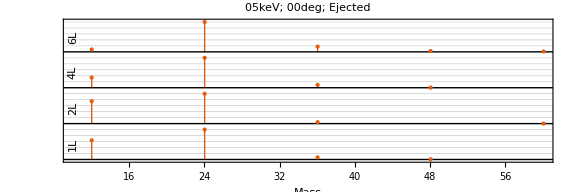
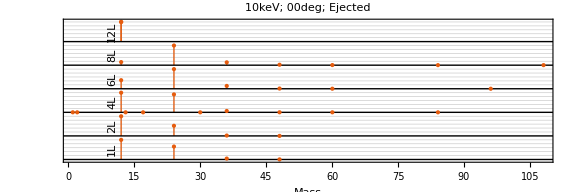
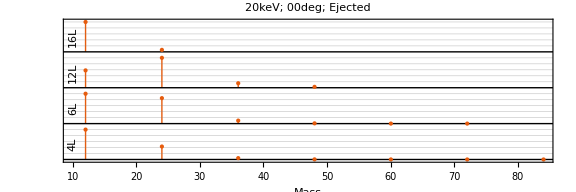
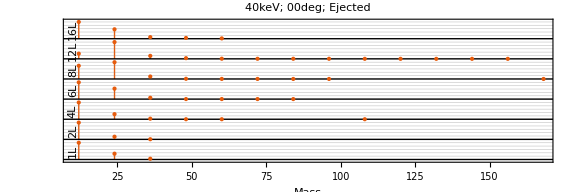

```mathematica
Table[
aaa=Table[
Show[
{
ListPlot[
Transpose[{data[layerssweep⟦j,i⟧]["results"]["massspectrum"]["toprelative"]⟦;;,1⟧,data[layerssweep⟦j,i⟧]["results"]["massspectrum"]["toprelative"]⟦;;,2⟧+move[i]}],
massspectrumPlotTheme,
Filling->move[i],
PlotRange->{All,{move[i],All}}
],
Graphics[{Thin,InfiniteLine[{{0,move[i]},{50,move[i]}}]}],
Graphics[Text[layerssweep⟦j,i,2⟧,{10,move[i]+0.5},{0,0},{0,1},Background->White]]
}
],
{i,Length[layerssweep⟦j⟧]}
];

Show[
aaa,
PlotRange->All,
GridLines->{None,Flatten[Table[Range[move[i]+0.2,move[i]+1,0.2],{i,1,Length[aaa],1}]]},
FrameTicks->{Automatic,None},
AspectRatio->1/3,
PlotLabel->StringJoin[Riffle[Flatten[{layerssweep⟦j,1,{1,3}⟧,{"Ejected"}}],"; "]],
ImageSize->Large
],
{j,Length[layerssweep]}]
```

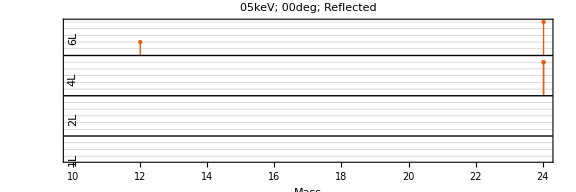
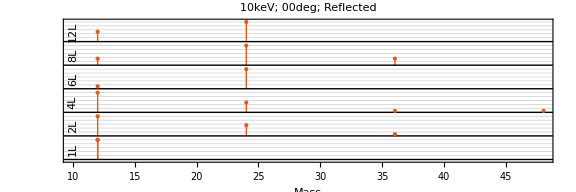
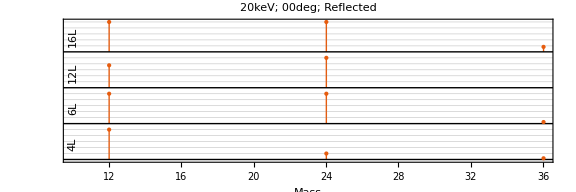
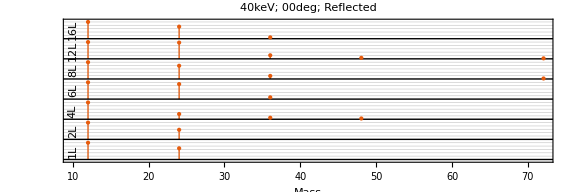

```mathematica
Table[
aaa=Table[
Show[
{
ListPlot[
Transpose[{data[layerssweep⟦j,i⟧]["results"]["massspectrum"]["bottomrelative"]⟦;;,1⟧,data[layerssweep⟦j,i⟧]["results"]["massspectrum"]["bottomrelative"]⟦;;,2⟧+move[i]}],
massspectrumPlotTheme,
Filling->move[i],
PlotRange->{All,{move[i],All}}
],
Graphics[{Thin,InfiniteLine[{{0,move[i]},{50,move[i]}}]}],
Graphics[Text[layerssweep⟦j,i,2⟧,{10,move[i]+0.5},{0,0},{0,1},Background->White]]
}
],
{i,Length[layerssweep⟦j⟧]}
];

Show[
aaa,
PlotRange->All,
GridLines->{None,Flatten[Table[Range[move[i]+0.2,move[i]+1,0.2],{i,1,Length[aaa],1}]]},
FrameTicks->{Automatic,None},
AspectRatio->1/3,
PlotLabel->StringJoin[Riffle[Flatten[{layerssweep⟦j,1,{1,3}⟧,{"Reflected"}}],"; "]],
ImageSize->Large
],
{j,Length[layerssweep]}]
```

```mathematica
layerssweep45
```

{{{10keV,1L,45deg},{10keV,2L,45deg},{10keV,4L,45deg},{10keV,6L,45deg}},{{40keV,1L,45deg},{40keV,2L,45deg},{40keV,4L,45deg},{40keV,8L,45deg},{40keV,12L,45deg},{40keV,16L,45deg}}}

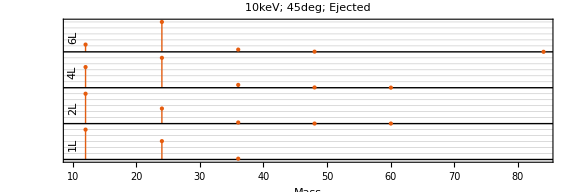
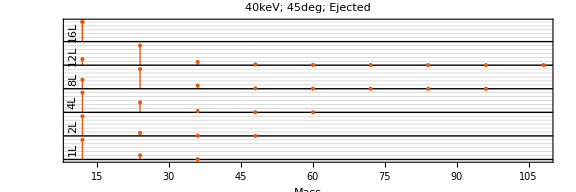

```mathematica
Table[
aaa=Table[
Show[
{
ListPlot[
Transpose[{data[layerssweep45⟦j,i⟧]["results"]["massspectrum"]["toprelative"]⟦;;,1⟧,data[layerssweep45⟦j,i⟧]["results"]["massspectrum"]["toprelative"]⟦;;,2⟧+move[i]}],
massspectrumPlotTheme,
Filling->move[i],
PlotRange->{All,{move[i],All}}
],
Graphics[{Thin,InfiniteLine[{{0,move[i]},{50,move[i]}}]}],
Graphics[Text[layerssweep45⟦j,i,2⟧,{10,move[i]+0.5},{0,0},{0,1},Background->White]]
}
],
{i,Length[layerssweep45⟦j⟧]}
];

Show[
aaa,
PlotRange->All,
GridLines->{None,Flatten[Table[Range[move[i]+0.2,move[i]+1,0.2],{i,1,Length[aaa],1}]]},
FrameTicks->{Automatic,None},
AspectRatio->1/3,
PlotLabel->StringJoin[Riffle[Flatten[{layerssweep45⟦j,1,{1,3}⟧,{"Ejected"}}],"; "]],
ImageSize->Large
],
{j,Length[layerssweep45]}]
```

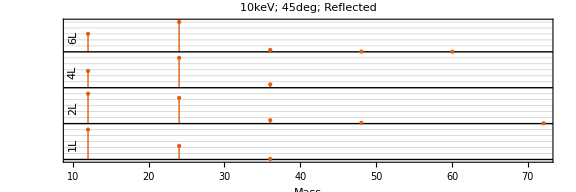
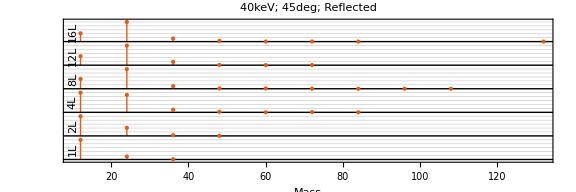

```mathematica
Table[
aaa=Table[
Show[
{
ListPlot[
Transpose[{data[layerssweep45⟦j,i⟧]["results"]["massspectrum"]["bottomrelative"]⟦;;,1⟧,data[layerssweep45⟦j,i⟧]["results"]["massspectrum"]["bottomrelative"]⟦;;,2⟧+move[i]}],
massspectrumPlotTheme,
Filling->move[i],
PlotRange->{All,{move[i],All}}
],
Graphics[{Thin,InfiniteLine[{{0,move[i]},{50,move[i]}}]}],
Graphics[Text[layerssweep45⟦j,i,2⟧,{10,move[i]+0.5},{0,0},{0,1},Background->White]]
}
],
{i,Length[layerssweep45⟦j⟧]}
];

Show[
aaa,
PlotRange->All,
GridLines->{None,Flatten[Table[Range[move[i]+0.2,move[i]+1,0.2],{i,1,Length[aaa],1}]]},
FrameTicks->{Automatic,None},
AspectRatio->1/3,
PlotLabel->StringJoin[Riffle[Flatten[{layerssweep45⟦j,1,{1,3}⟧,{"Reflected"}}],"; "]],
ImageSize->Large
],
{j,Length[layerssweep45]}]
```

```mathematica
anglessweep
```

{{{10keV,2L,00deg},{10keV,2L,15deg},{10keV,2L,30deg},{10keV,2L,45deg},{10keV,2L,50deg},{10keV,2L,55deg},{10keV,2L,60deg},{10keV,2L,65deg},{10keV,2L,70deg},{10keV,2L,75deg},{10keV,2L,80deg}},{{40keV,2L,00deg},{40keV,2L,15deg},{40keV,2L,30deg},{40keV,2L,45deg},{40keV,2L,55deg},{40keV,2L,60deg},{40keV,2L,65deg},{40keV,2L,70deg},{40keV,2L,75deg},{40keV,2L,77deg},{40keV,2L,80deg}}}

```mathematica
move[i_]:=(i-1)*1.2;
```

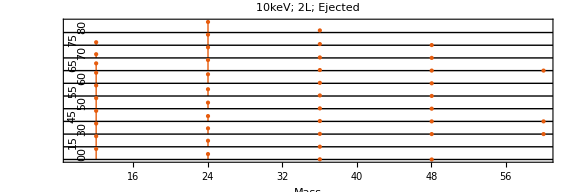
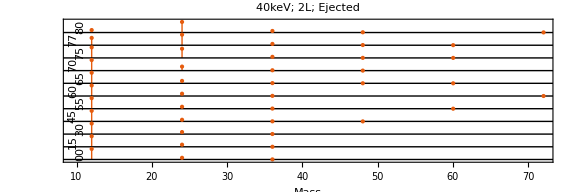

```mathematica
Table[
aaa=Table[
Show[
{
ListPlot[
Transpose[{data[anglessweep⟦j,i⟧]["results"]["massspectrum"]["toprelative"]⟦;;,1⟧,data[anglessweep⟦j,i⟧]["results"]["massspectrum"]["toprelative"]⟦;;,2⟧+move[i]}],
massspectrumPlotTheme,
Filling->move[i],
PlotRange->{All,{move[i],All}}
],
Graphics[{Thin,InfiniteLine[{{0,move[i]},{50,move[i]}}]}],
Graphics[Text[StringTake[anglessweep⟦j,i,3⟧,2],{10-If[EvenQ[i],0.5,-0.5],move[i]+0.5},{0,0},{0,1},Background->White]]
}
],
{i,Length[anglessweep⟦j⟧]}
];

Show[
aaa,
PlotRange->All,
GridLines->{None,Flatten[Table[Range[move[i]+0.2,move[i]+1,0.2],{i,1,Length[aaa],1}]]},
FrameTicks->{Automatic,None},
AspectRatio->1/3,
PlotLabel->StringJoin[Riffle[Flatten[{anglessweep⟦j,1,{1,2}⟧,{"Ejected"}}],"; "]],
ImageSize->Large
],
{j,Length[anglessweep]}]
```

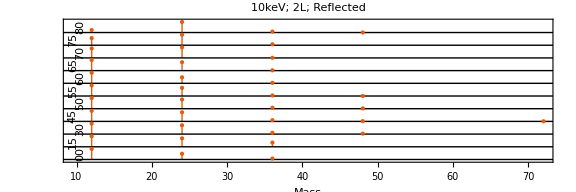
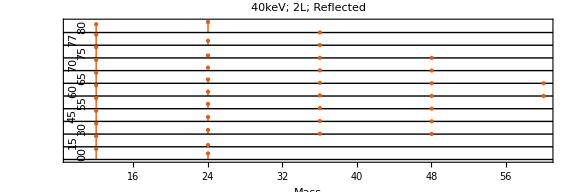

```mathematica
Table[
aaa=Table[
Show[
{
ListPlot[
Transpose[{data[anglessweep⟦j,i⟧]["results"]["massspectrum"]["bottomrelative"]⟦;;,1⟧,data[anglessweep⟦j,i⟧]["results"]["massspectrum"]["bottomrelative"]⟦;;,2⟧+move[i]}],
massspectrumPlotTheme,
Filling->move[i],
PlotRange->{All,{move[i],All}}
],
Graphics[{Thin,InfiniteLine[{{0,move[i]},{50,move[i]}}]}],
Graphics[Text[StringTake[anglessweep⟦j,i,3⟧,2],{10-If[EvenQ[i],0.5,-0.5],move[i]+0.5},{0,0},{0,1},Background->White]]
}
],
{i,Length[anglessweep⟦j⟧]}
];

Show[
aaa,
PlotRange->All,
GridLines->{None,Flatten[Table[Range[move[i]+0.2,move[i]+1,0.2],{i,1,Length[aaa],1}]]},
FrameTicks->{Automatic,None},
AspectRatio->1/3,
PlotLabel->StringJoin[Riffle[Flatten[{anglessweep⟦j,1,{1,2}⟧,{"Reflected"}}],"; "]],
ImageSize->Large
],
{j,Length[anglessweep]}]
```

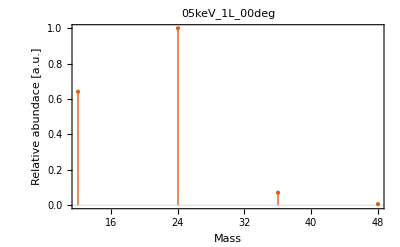
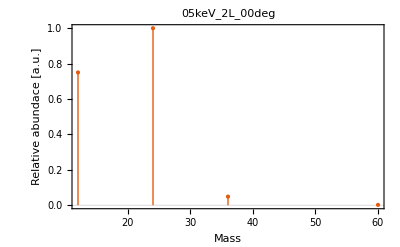
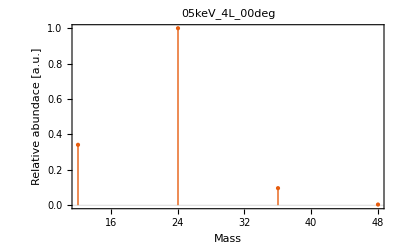
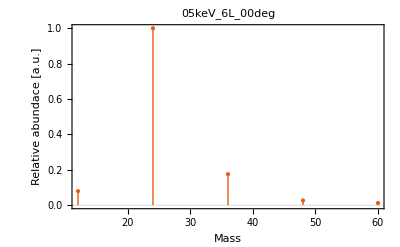
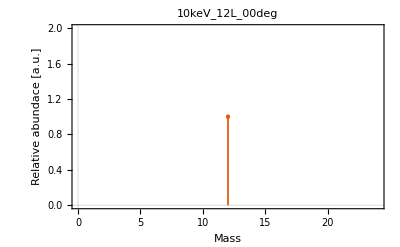
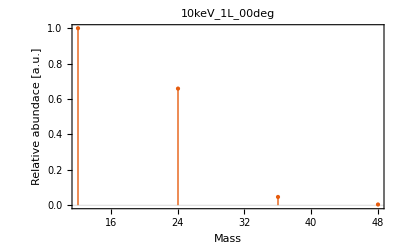
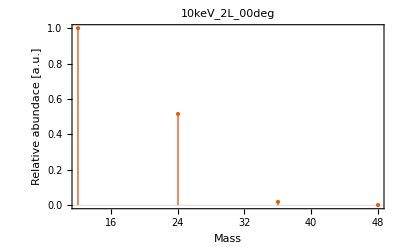
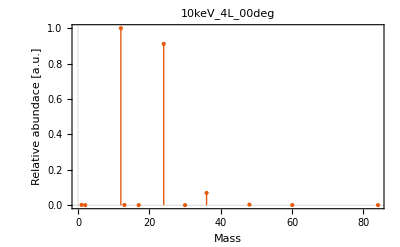

```mathematica
Table[
ListPlot[
data[datakeys⟦i⟧]["results"]["massspectrum"]["toprelative"],
massspectrumPlotTheme,
PlotLabel->StringJoin[Riffle[datakeys⟦i⟧,"_"]]
],
{i,Length[datakeys]}
]
```

#### Plot angular distributions

```mathematica
angledistPlotTheme={
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
FrameLabel->{"Angle [deg]","Relative abundace [a.u.]"}
};
```

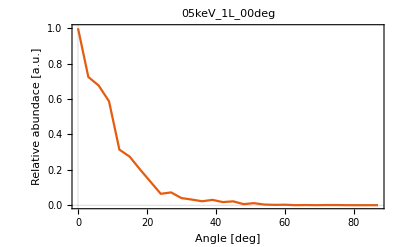
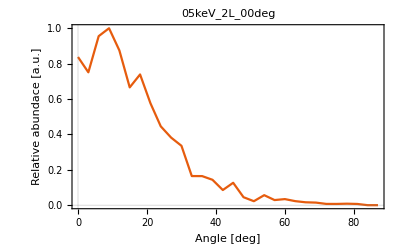
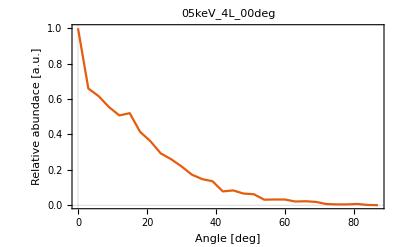
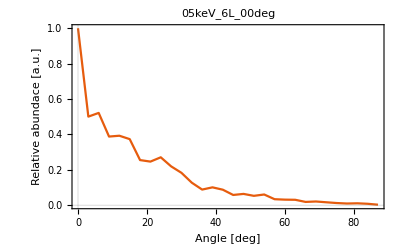
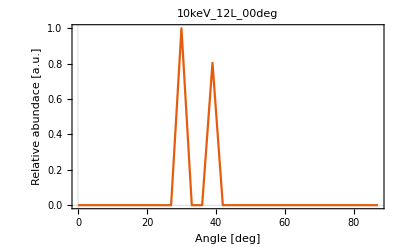
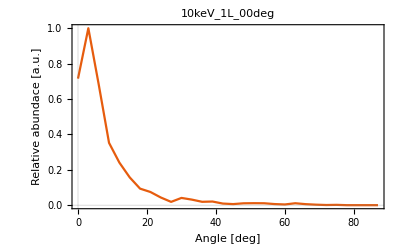
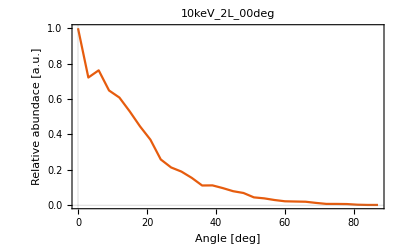
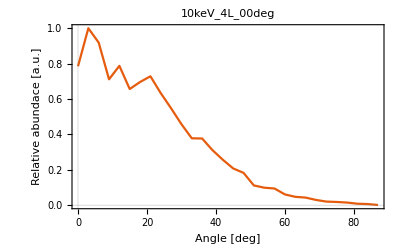
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
ListPlot[
data[datakeys⟦i⟧]["results"]["angledist"]["toprelative"]["all"],
angledistPlotTheme,
PlotLabel->StringJoin[Riffle[datakeys⟦i⟧,"_"]]
],
{i,Length[datakeys]}
]
```

#### Plot energy distributions

```mathematica
energiesPlotTheme={
PlotTheme->"Scientific",
PlotRange->All,
FrameLabel->{"Energy [eV]","Number of molecules [a.u.]"}
};
```

```mathematica
Table[
Histogram[
data[datakeys⟦i⟧]["results"]["energies"]["top"]["total"],
{10},
energiesPlotTheme,
PlotLabel->StringJoin[Riffle[datakeys⟦i⟧,"_"]]
],
{i,Length[datakeys]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*SetDirectory[NotebookDirectory[]]*)
```